## Electricity Data

Measures: Heating degree days.,

Build the electricity price by state in time database.
Data from: https://www.eia.gov/electricity/monthly/epm_table_grapher.php?t=epmt_5_06_a

Substitution rules for states to entities:

```mathematica
stateEntitiesRule = {"New England"->None,"Connecticut"->Entity["AdministrativeDivision",{"Connecticut","UnitedStates"}],"Maine"->Entity["AdministrativeDivision",{"Maine","UnitedStates"}],"Massachusetts"->Entity["AdministrativeDivision",{"Massachusetts","UnitedStates"}],"New Hampshire"->Entity["AdministrativeDivision",{"NewHampshire","UnitedStates"}],"Rhode Island"->Entity["AdministrativeDivision",{"RhodeIsland","UnitedStates"}],"Vermont"->Entity["AdministrativeDivision",{"Vermont","UnitedStates"}],"Middle Atlantic"->None,"New Jersey"->Entity["AdministrativeDivision",{"NewJersey","UnitedStates"}],"New York"->Entity["AdministrativeDivision",{"NewYork","UnitedStates"}],"Pennsylvania"->Entity["AdministrativeDivision",{"Pennsylvania","UnitedStates"}],"East North Central"->None,"Illinois"->Entity["AdministrativeDivision",{"Illinois","UnitedStates"}],"Indiana"->Entity["AdministrativeDivision",{"Indiana","UnitedStates"}],"Michigan"->Entity["AdministrativeDivision",{"Michigan","UnitedStates"}],"Ohio"->Entity["AdministrativeDivision",{"Ohio","UnitedStates"}],"Wisconsin"->Entity["AdministrativeDivision",{"Wisconsin","UnitedStates"}],"West North Central"->None,"Iowa"->Entity["AdministrativeDivision",{"Iowa","UnitedStates"}],"Kansas"->Entity["AdministrativeDivision",{"Kansas","UnitedStates"}],"Minnesota"->Entity["AdministrativeDivision",{"Minnesota","UnitedStates"}],"Missouri"->Entity["AdministrativeDivision",{"Missouri","UnitedStates"}],"Nebraska"->Entity["AdministrativeDivision",{"Nebraska","UnitedStates"}],"North Dakota"->Entity["AdministrativeDivision",{"NorthDakota","UnitedStates"}],"South Dakota"->Entity["AdministrativeDivision",{"SouthDakota","UnitedStates"}],"South Atlantic"->None,"Delaware"->Entity["AdministrativeDivision",{"Delaware","UnitedStates"}],"District of Columbia"->Entity["AdministrativeDivision",{"DistrictOfColumbia","UnitedStates"}],"Florida"->Entity["AdministrativeDivision",{"Florida","UnitedStates"}],"Georgia"->Entity["AdministrativeDivision",{"Georgia","UnitedStates"}],"Maryland"->Entity["AdministrativeDivision",{"Maryland","UnitedStates"}],"North Carolina"->Entity["AdministrativeDivision",{"NorthCarolina","UnitedStates"}],"South Carolina"->Entity["AdministrativeDivision",{"SouthCarolina","UnitedStates"}],"Virginia"->Entity["AdministrativeDivision",{"Virginia","UnitedStates"}],"West Virginia"->Entity["AdministrativeDivision",{"WestVirginia","UnitedStates"}],"East South Central"->None,"Alabama"->Entity["AdministrativeDivision",{"Alabama","UnitedStates"}],"Kentucky"->Entity["AdministrativeDivision",{"Kentucky","UnitedStates"}],"Mississippi"->Entity["AdministrativeDivision",{"Mississippi","UnitedStates"}],"Tennessee"->Entity["AdministrativeDivision",{"Tennessee","UnitedStates"}],"West South Central"->None,"Arkansas"->Entity["AdministrativeDivision",{"Arkansas","UnitedStates"}],"Louisiana"->Entity["AdministrativeDivision",{"Louisiana","UnitedStates"}],"Oklahoma"->Entity["AdministrativeDivision",{"Oklahoma","UnitedStates"}],"Texas"->Entity["AdministrativeDivision",{"Texas","UnitedStates"}],"Mountain"->None,"Arizona"->Entity["AdministrativeDivision",{"Arizona","UnitedStates"}],"Colorado"->Entity["AdministrativeDivision",{"Colorado","UnitedStates"}],"Idaho"->Entity["AdministrativeDivision",{"Idaho","UnitedStates"}],"Montana"->Entity["AdministrativeDivision",{"Montana","UnitedStates"}],"Nevada"->Entity["AdministrativeDivision",{"Nevada","UnitedStates"}],"New Mexico"->Entity["AdministrativeDivision",{"NewMexico","UnitedStates"}],"Utah"->Entity["AdministrativeDivision",{"Utah","UnitedStates"}],"Wyoming"->Entity["AdministrativeDivision",{"Wyoming","UnitedStates"}],"Pacific Contiguous"->None,"California"->Entity["AdministrativeDivision",{"California","UnitedStates"}],"Oregon"->Entity["AdministrativeDivision",{"Oregon","UnitedStates"}],"Washington"->Entity["AdministrativeDivision",{"Washington","UnitedStates"}],"Pacific Noncontiguous"->None,"Alaska"->Entity["AdministrativeDivision",{"Alaska","UnitedStates"}],"Hawaii"->Entity["AdministrativeDivision",{"Hawaii","UnitedStates"}],"U.S. Total"->None};
```

```mathematica
residential = 2;
commercial = 4;
industrial = 6;
directories = Select[FileNames["*",NotebookDirectory[]<>"ElectricityPrices"],FileType[#]==Directory&];
database = Table[
data = First[Import[d<>"/Table_5_06_A.xlsx"]];
date = DateObject[data[[4,2]]];
statesAndPrices = Take[data,{5,-3}];
entityStates = statesAndPrices[[All,1]] /. stateEntitiesRule;
statePrices =  DeleteCases[Transpose[{entityStates,statesAndPrices[[All,industrial]]}],{None,_}|{__String}];
{date,statePrices}

,{d,directories}
];
database = SortBy[database,First];
Export[NotebookDirectory[]<>"electricity_prices_by_state_and_date.mx",database]
```

/home/carlos/Documentos/Wolfram_School/Project/database/electricity_prices_by_state_and_date.mx

Since the format of this database is inconvenient for times series processing I will reshape it. I will keep the original database for the GeoRegionValuePlots.Also I will delete the states that are not present in the Degree Days database.

```mathematica
states = database[[1,2,All,1]];
databasets = Table[{First[database[[All,2,i,1]]],Transpose[{database[[All,1]],database[[All,2,i]][[All,2]]}]},{i,1,Length[states]}];
databasets = DeleteCases[databasets,{Entity["AdministrativeDivision",{"Alaska","UnitedStates"}],_}|{Entity["AdministrativeDivision",{"DistrictOfColumbia","UnitedStates"}],_}|{Entity["AdministrativeDivision",{"Hawaii","UnitedStates"}],_}];
databasets = SortBy[databasets,First];
states = databasets[[All,1]];
```

```mathematica
Export[NotebookDirectory[]<>"electricity_prices_by_state_and_date_forTS.mx",databasets]
```

/home/carlos/Documentos/Wolfram_School/Project/database/electricity_prices_by_state_and_date_forTS.mx

Load database

```mathematica
database = Import[NotebookDirectory[]<>"industrial_electricity_prices_by_state_and_date.mx"];
```

Visualization of electricity prices by date

```mathematica
ListAnimate[Map[GeoRegionValuePlot[#[[2]],PlotLabel->DateString[#[[1]]],ImageSize->500,ColorFunctionScaling->False,ColorFunction->(ColorData["Rainbow"][Log[#/15+1]]&)]&,database]]
```

Average electricity price by date by state

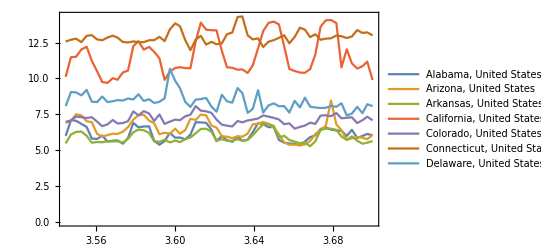

```mathematica
pltData = Take[databasets,7];
DateListPlot[pltData[[All,2]],PlotLegends->pltData[[All,1]]]
```

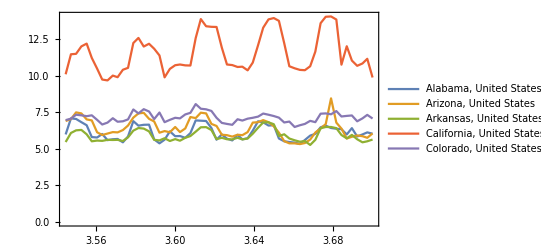
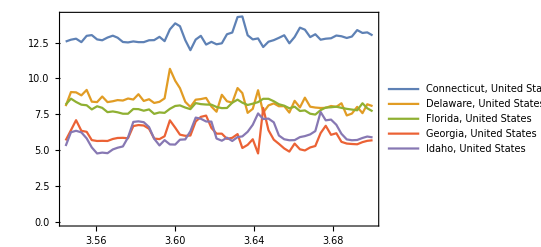
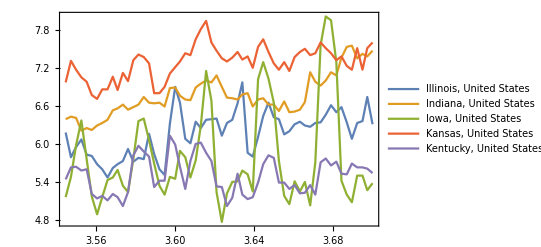
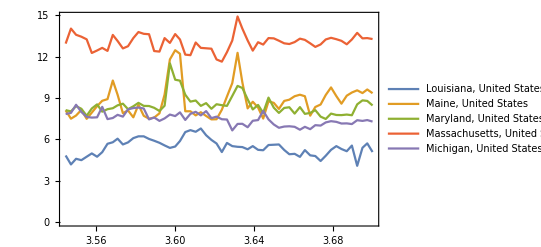
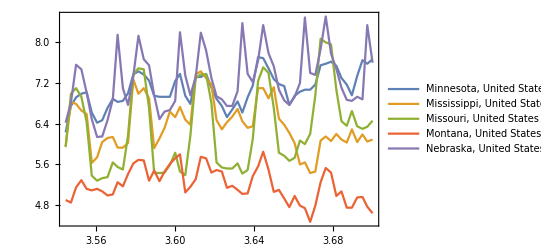
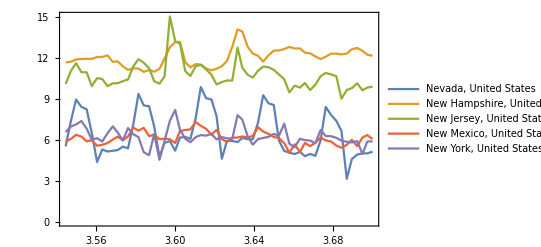
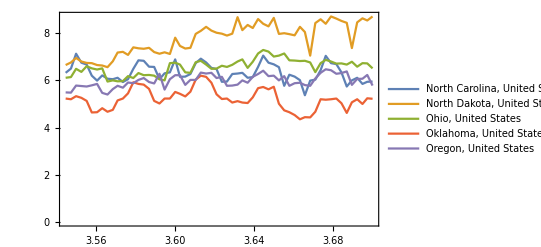
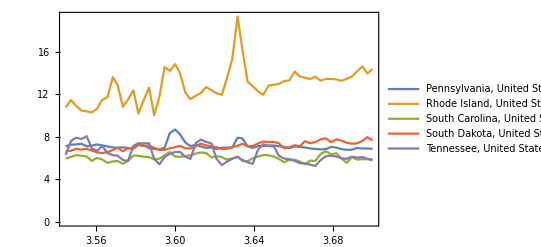
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
plots = Map[DateListPlot[#[[All,2]],PlotLegends->#[[All,1]]]&,Partition[databasets,5]];
Grid[Partition[plots,UpTo[3]],Frame->All]
```

Total average price

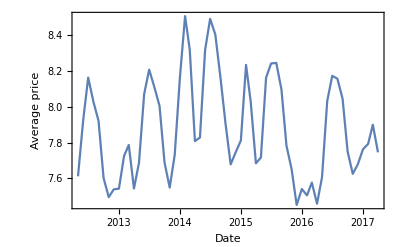

```mathematica
DateListPlot[Map[{#[[1]],Mean[#[[2,All,2]]]}&,database],FrameLabel->{"Date","Average price"},PlotRange->Full]
```

Correlation matrix of electricity prices

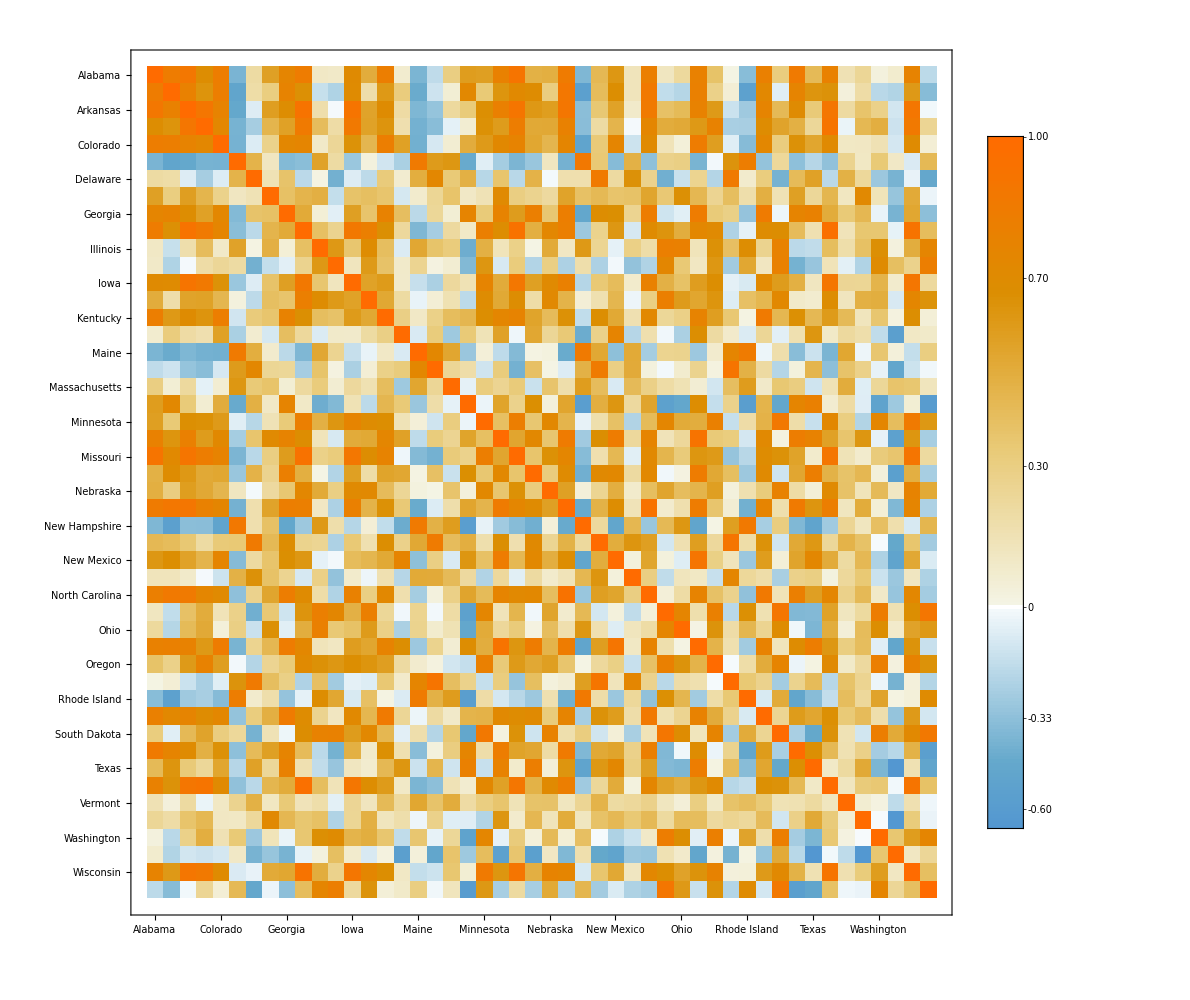

```mathematica
stateNames = Map[StringDelete[EntityValue[#,"Name"],", United States"]&,databasets[[All,1]]];
prices = databasets[[All,2,All,2]];
corrMatrix = Correlation[Transpose[prices]];
MatrixPlot[corrMatrix,FrameTicks->{{Transpose[{Range[Length[stateNames]],stateNames}],None},{Transpose[{Range[Length[stateNames]],Map[Rotate[#,90 Degree]&,stateNames]}],None}},PlotLegends->Automatic,ImageSize->1000]
```

```mathematica
Through[{Min,Max}[Flatten[corrMatrix]/.(x_/;x>0.99)->0.0]]
```

{-0.659422,0.904786}

Why some states have high correlation?

- Hypothesis: States that are closer have higher correlation.

Let’s define a high correlation as one that is greater than 0.7. I will focus on positive correlation because the is no significant negative correlations.

```mathematica
states = databasets[[All,1]];
niceCorr = Position[corrMatrix-IdentityMatrix[Length[corrMatrix]],x_/;x>0.7];
niceCorr = DeleteDuplicates[Map[Sort,niceCorr]];
corrStates = Map[{states[[#[[1]]]],states[[#[[2]]]]}&,niceCorr];

Manipulate[GeoListPlot[corrStates[[i]]],{i,1,Length[corrStates],1},SaveDefinitions->True]
```

Almost half of the cases that have high correlation can be explained by geographic distance.

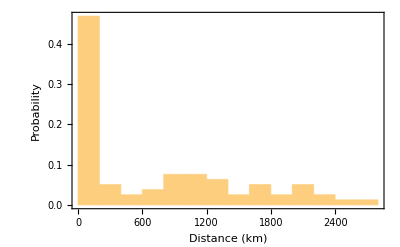

```mathematica
Histogram[Map[QuantityMagnitude[GeoDistance[#,UnitSystem->"km"]]&,corrStates],10,"Probability",Frame->True,FrameLabel->{"Distance (km)","Probability"}]
```

- Hypothesis: States that share the same electrical grid have correlated prices.

The United States electrical grid is divided in 8 separated regions by the North American Electric Reliability Corporation (NERC).

Maybe use a weighted average or another kind of measure to obtain the coordinates

From this data alone a predictor may be constructed

The data of the coordinates of each grid was obtained from: https://public.opendatasoft.com/explore/dataset/nerc-regions/export/?flg=fr

```mathematica
nerc = Import[NotebookDirectory[]<>"nerc-regions.kml", "Data"];
```

To see if states sharing the same grid have correlated prices we can plot the correlated states with the grid map as background

```mathematica
nercAreas = Map[{EdgeForm[{Red,Dashed}],RandomColor[],#}&,nerc[[1,2,2]]];
nercAreasPlot = GeoGraphics[nercAreas];
plts = Table[
Image[
Show[
GeoListPlot[corrStates[[i]],PlotStyle->Directive[EdgeForm[Thickness[0.009]]]],
nercAreasPlot,
GeoRange->1.5*GeoDistance[Map[EntityValue[#,"Coordinates"]&,corrStates[[i]]]],
GeoCenter->Mean[Map[EntityValue[#,"Coordinates"]&,corrStates[[i]]]]
]
]
,{i,1,Length[corrStates],1}];

Manipulate[
Legended[
plts[[i]]
,LineLegend[{Directive[Dashed,Red],Directive[Thick,Black]},{"Nerc Areas","Correlated states"}]
]
,{i,1,Length[plts],1},SaveDefinitions->True
]
```

Only 35% of the high correlated states share the same grid.

```mathematica
nercAreasUnformatted = nerc[[1,2,2]];
corrNerc = Table[
corrStatesCoord = Map[EntityValue[#,"Coordinates"]&,c];
nercAreaMatch = Map[Apply[Or,GeoWithinQ[#,First[corrStatesCoord]]] && Apply[Or,GeoWithinQ[#,Last[corrStatesCoord]]]&,nercAreasUnformatted];
Apply[Or,nercAreaMatch],
{c,corrStates}
];
```

```mathematica
N[Total[corrNerc /.{True->1,False->0}]/Length[corrNerc]]
```

0.35443

## Heating degree days data

```mathematica
directories = Select[FileNames["*",NotebookDirectory[]<>"DegreeDays"],FileType[#]==Directory&];

heatingDegreesByStateWDates = Table[
txt = Import[d<>"/StatesCONUS.Heating.txt"];
lines = StringSplit[txt,"\n"];
dateStrings = Drop[StringSplit[lines[[4]],"|"],1];
dates = Map[DateObject,dateStrings];
stateAndHDays = Map[StringSplit[#,"|"]&,Drop[lines,4]];
states = Map[Interpreter["AdministrativeDivision"],stateAndHDays[[All,1]]];
hdays = Map[Drop[#,1]&,stateAndHDays];
datesAndHeatingDays = Map[Transpose[{dates,ToExpression[#]}]&,hdays];

datesAndHeatingDaysByMonth = Table[
gatheredByMonth = GatherBy[dh,DateValue[First[#],"Month"]&];
Map[{FullDateToMonth[#[[1,1]]],Total[#[[All,2]]]}&,gatheredByMonth]
,{dh,datesAndHeatingDays}
];

Transpose[{states,datesAndHeatingDaysByMonth}]
,{d,directories}
];
```

```mathematica
transposedHD =Transpose[heatingDegreesByStateWDates];
formattedHeatingDegreesByStateWDates = Table[{t[[1,1]],Flatten[t[[All,2]],1]},{t,transposedHD}];
```

```mathematica
Export[NotebookDirectory[]<>"heating_degree_days_by_state_and_date.mx",formattedHeatingDegreesByStateWDates]
```

/home/carlos/Documentos/Wolfram_School/Project/database/heating_degree_days_by_state_and_date.mx

```mathematica
formattedHeatingDegreesByStateWDates = Import[NotebookDirectory[]<>"heating_degree_days_by_state_and_date.mx"];
```

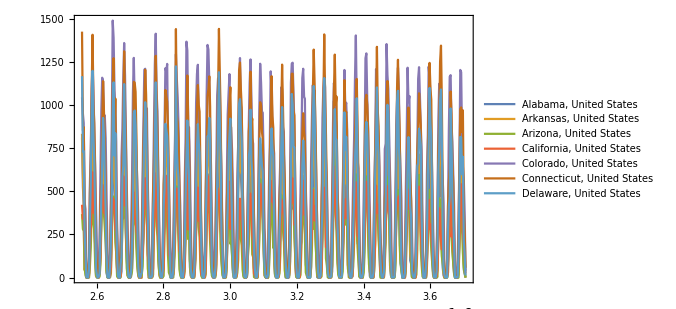

```mathematica
pltData = Take[formattedHeatingDegreesByStateWDates,7];
DateListPlot[pltData[[All,2]],PlotLegends->pltData[[All,1]],ImageSize->500,PlotRange->Full]
```

## Cooling degree days data

```mathematica
directories = Select[FileNames["*",NotebookDirectory[]<>"DegreeDays"],FileType[#]==Directory&];

coolingDegreesByStateWDates = Table[
txt = Import[d<>"/StatesCONUS.Cooling.txt"];
lines = StringSplit[txt,"\n"];
dateStrings = Drop[StringSplit[lines[[4]],"|"],1];
dates = Map[DateObject,dateStrings];
stateAndHDays = Map[StringSplit[#,"|"]&,Drop[lines,4]];
states = Map[Interpreter["AdministrativeDivision"],stateAndHDays[[All,1]]];
hdays = Map[Drop[#,1]&,stateAndHDays];
datesAndCoolingDays = Map[Transpose[{dates,ToExpression[#]}]&,hdays];

datesAndCoolingDaysByMonth = Table[
gatheredByMonth = GatherBy[dh,DateValue[First[#],"Month"]&];
Map[{FullDateToMonth[#[[1,1]]],Total[#[[All,2]]]}&,gatheredByMonth]
,{dh,datesAndCoolingDays}
];

Transpose[{states,datesAndCoolingDaysByMonth}]
,{d,directories}
];
transposedHD =Transpose[coolingDegreesByStateWDates];
formattedCoolingDegreesByStateWDates = Table[{t[[1,1]],Flatten[t[[All,2]],1]},{t,transposedHD}];
```

```mathematica
Export[NotebookDirectory[]<>"cooling_degree_days_by_state_and_date.mx",formattedCoolingDegreesByStateWDates]
```

/home/carlos/Documentos/Wolfram_School/Project/database/cooling_degree_days_by_state_and_date.mx

```mathematica
formattedCoolingDegreesByStateWDates = Import[NotebookDirectory[]<>"cooling_degree_days_by_state_and_date.mx"];
```

```mathematica
pltData = Take[formattedHeatingDegreesByStateWDates,7];
DateListPlot[pltData[[All,2]],PlotLegends->pltData[[All,1]],ImageSize->500,PlotRange->Full]
```

-Graphics-

## Match cooling and heating degree days to electricity price dates

```mathematica
SelectInDateRange[data_]:= Select[data,Last[database[[All,1]]]≥#[[1]]≥ First[database[[All,1]]]&];
hdMatching = Map[{#[[1]],SelectInDateRange[#[[2]]]}&,formattedHeatingDegreesByStateWDates];
cdMatching = Map[{#[[1]],SelectInDateRange[#[[2]]]}&,formattedCoolingDegreesByStateWDates];
hdMatching = SortBy[hdMatching,First];
cdMatching = SortBy[cdMatching,First];
```

Advice: Write named functions

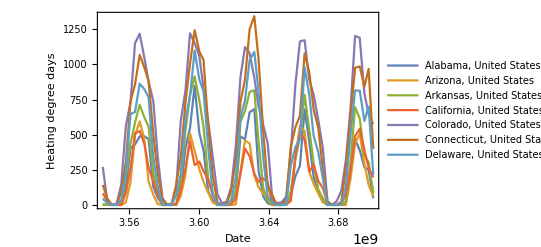

```mathematica
pltData = Take[hdMatching,7];
DateListPlot[pltData[[All,2]],FrameLabel->{"Date", "Heating degree days"},PlotLegends->pltData[[All,1]]]
```

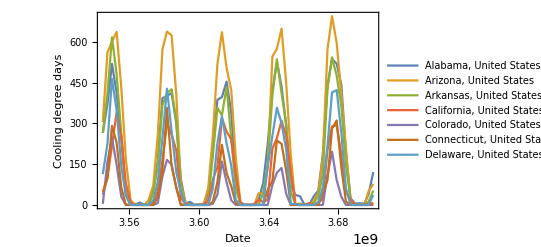

```mathematica
pltData = Take[cdMatching,7];
DateListPlot[pltData[[All,2]],FrameLabel->{"Date", "Cooling degree days"},PlotLegends->pltData[[All,1]]]
```

Bad assumption: The heating and cooling mean the same rate of electricity consumption

```mathematica
DateListPlot[Map[{#[[1]],Mean[#[[2,All,2]]]}&,database],FrameLabel->{"Date","Average price"},PlotRange->Full]
```

-Graphics-

Consider base demand

## Correlation between degree days and electricity prices

```mathematica
state = 1;
degreeDays = 0.2hdMatching[[state,2,All,2]]+cdMatching[[state,2,All,2]];
prices = databasenew[[state,2,All,2]];
```

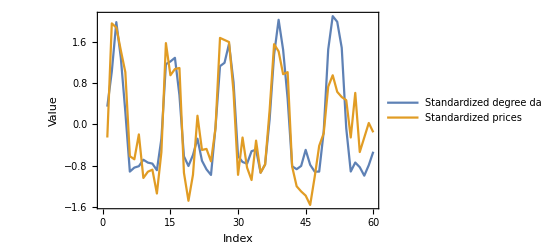

```mathematica
ListLinePlot[{Standardize[degreeDays],Standardize[prices]},Frame->True,FrameLabel->{"Index","Value"},PlotLegends->{"Standardized degree days","Standardized prices"}]
```

```mathematica
Correlation[degreeDays,prices]
```

0.853118

Let’s suppose two “strengths” α and β of the demand caused by heating degree days and cooling degree days. I can assign (by guess) values to α and β such as 0.2 and 1.0 respectively.

```mathematica
α = 0.2; β = 1.0;
state = 1;
degreeDays = α hdMatching[[state,2,All,2]]+β cdMatching[[state,2,All,2]];
prices = databasets[[state,2,All,2]];
```

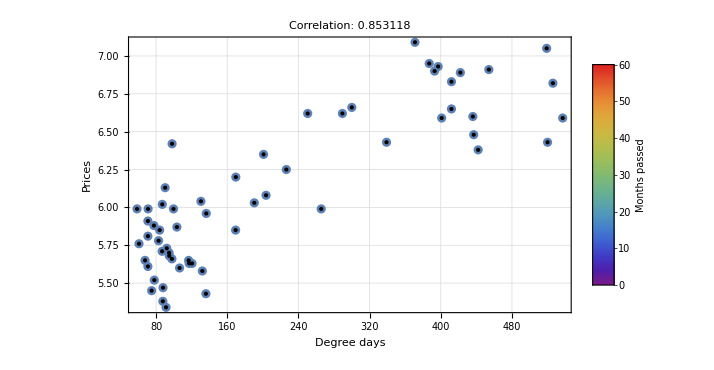

```mathematica
dates = hdMatching[[1,2,All,1]];
pltData = Transpose[{degreeDays,prices}];
coloredPoints =  Transpose[{Transpose[{degreeDays,prices}],Table[Hue[QuantityMagnitude[d-First[dates]]/Length[dates]],{d,dates}]}];
styledPoints = Map[Apply[Style,#]&,coloredPoints];

Legended[
ListPlot[styledPoints,PlotRange->All,GridLines->Automatic,Frame->True,FrameLabel->{"Degree days","Prices"},ImageSize->600,PlotLabel->"Correlation: "<>ToString[Correlation[degreeDays,prices]]],
Placed[BarLegend[{"Rainbow",{0,Length[dates]}},LegendLabel->"Months passed"],Right]
]
```

Fit the curve

```mathematica
fit = LinearModelFit[Transpose[{degreeDays,prices}],{1,x},x]
```

FittedModel[5.53397+0.00274246 x]

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 5.53397 | 0.057672 | 95.9559 | 1.31774×10^-65
x | 0.00274246 | 0.000220218 | 12.4534 | 4.96497×10^-18

```mathematica
fit["RSquared"]
```

0.727811

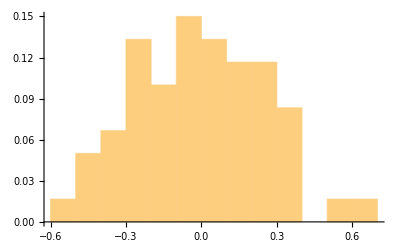

```mathematica
Histogram[fit["FitResiduals"],15,"Probability"]
```

I will search now the optimum values of α and β. Method 1

```mathematica
stateαβparams = Table[
prices = databasenew[[s,2,All,2]];
αβtbl = Table[
degreeDays = α hdMatching[[state,2,All,2]]+β cdMatching[[state,2,All,2]];
{α,β,Correlation[degreeDays,prices]}
,{α,0.1,1,0.1},{β,0.1,1,0.1}
];
{states[[s]],First[MaximalBy[Flatten[αβtbl,1],Last]]}
,{s,1,Length[states]}
];
```

```mathematica
GeoRegionValuePlot[Transpose[{stateαβparams[[All,1]],stateαβparams[[All,2]][[All,1]]}],ColorFunction->"SolarColors",PlotLabel->"Heating degree days"]
GeoRegionValuePlot[Transpose[{stateαβparams[[All,1]],stateαβparams[[All,2]][[All,2]]}],ColorFunction->"DeepSeaColors",PlotLabel->"Cooling degree days"]
```

-Graphics-

-Graphics-

Method 2

```mathematica
stateαβparams = Table[
prices = databasenew[[s,2,All,2]];
{α, β} = {Correlation[hdMatching[[state,2,All,2]],prices],Correlation[cdMatching[[state,2,All,2]],prices]};
{states[[s]],{α,β}}
,{s,1,Length[states]}
];
```

```mathematica
stateαβparams
```

{{Alabama, United States,{-0.585528,0.853801}},{Arizona, United States,{-0.25468,0.222454}},{Arkansas, United States,{-0.6314,0.807265}},{California, United States,{-0.586684,0.883915}},{Colorado, United States,{-0.580281,0.724878}},{Connecticut, United States,{-0.607257,0.693472}},{Delaware, United States,{0.49407,-0.450272}},{Florida, United States,{0.333161,-0.0435456}},{Georgia, United States,{0.0898969,-0.0871008}},{Idaho, United States,{-0.170317,0.379036}},{Illinois, United States,{-0.227993,0.609223}},{Indiana, United States,{0.0538062,0.0402373}},{Iowa, United States,{-0.663567,0.837784}},{Kansas, United States,{-0.0256128,0.091508}},{Kentucky, United States,{-0.0287902,-0.0337084}},{Louisiana, United States,{-0.50373,0.815653}},{Maine, United States,{-0.331209,0.439311}},{Maryland, United States,{-0.258731,0.569217}},{Massachusetts, United States,{-0.0814542,0.0440431}},{Michigan, United States,{0.670291,-0.433037}},{Minnesota, United States,{0.450773,-0.304675}},{Mississippi, United States,{0.066354,0.152806}},{Missouri, United States,{-0.224784,0.395951}},{Montana, United States,{-0.422327,0.52233}},{Nebraska, United States,{-0.274453,0.55049}},{Nevada, United States,{-0.642145,0.896623}},{New Hampshire, United States,{-0.117049,0.442682}},{New Jersey, United States,{-0.420844,0.494777}},{New Mexico, United States,{-0.592578,0.818607}},{New York, United States,{0.465318,-0.39984}},{North Carolina, United States,{0.135529,0.222918}},{North Dakota, United States,{-0.380138,0.458337}},{Ohio, United States,{0.130916,0.0464399}},{Oklahoma, United States,{-0.438339,0.776523}},{Oregon, United States,{-0.154373,0.182988}},{Pennsylvania, United States,{-0.065041,0.159469}},{Rhode Island, United States,{-0.433434,0.624642}},{South Carolina, United States,{-0.29089,0.399614}},{South Dakota, United States,{0.351121,-0.153339}},{Tennessee, United States,{0.500658,-0.351949}},{Texas, United States,{-0.241436,0.656288}},{Utah, United States,{-0.305648,0.309369}},{Vermont, United States,{-0.356041,0.598908}},{Virginia, United States,{-0.0693603,0.249408}},{Washington, United States,{-0.658003,0.815492}},{West Virginia, United States,{0.275419,0.0795791}},{Wisconsin, United States,{0.0522173,0.202349}},{Wyoming, United States,{-0.0020949,0.0717765}}}

## Import FRED II data

```mathematica
GetFredSeries[seriesname_]:=Module[{list=First/@Import["http://research.stlouisfed.org/fred2/series/"<>seriesname<>"/downloaddata/"<>seriesname<>".txt","TSV"],ts},
ts = ToExpression[
DeleteCases[#,{_,"."}]&@({StringSplit[#[[1]],"-"],#[[2]]}&/@StringSplit/@Drop[list,Position[list,_?(StringMatchQ[#,"DATE"~~Whitespace~~"VALUE"]&),Heads->False][[1,1]]])
];
Map[{DateObject[Take[#[[1]],2]],#[[2]]}&,ts]
];
```

Industrial production: Mining: Natural gas

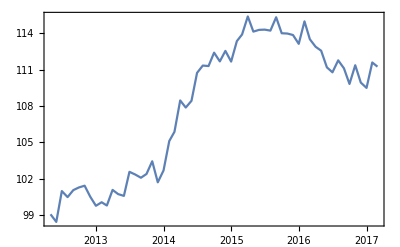

```mathematica
naturalGasData = GetFredSeries["IPN211111GN"];
naturalGasData = Select[naturalGasData,First[database][[1]]≤ #[[1]]≤ Last[database][[1]]&];
DateListPlot[naturalGasData]
```

Natural gas spot price

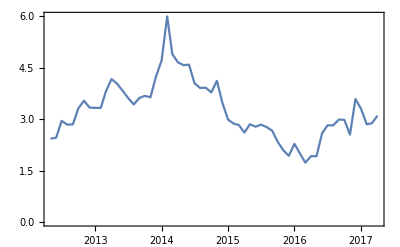

```mathematica
gasPrice = GetFredSeries["MHHNGSP"];
gasPrice = Select[gasPrice,First[database][[1]]≤ #[[1]]≤ Last[database][[1]]&];
DateListPlot[gasPrice]
```

Global price of coal: Australia

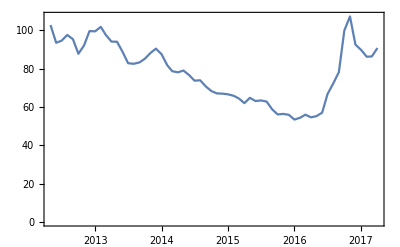

```mathematica
coalPrice = GetFredSeries["PCOALAUUSDM"];
coalPrice = Select[coalPrice,First[database][[1]]≤ #[[1]]≤ Last[database][[1]]&];
DateListPlot[coalPrice]
```